n0-h0^2 n1+n3 z-n4 z^2

2.5×10^-7

{{C1→0.+3.64964×10^-9 h0,C2→0.+1. h0}}

{0.+3.64964×10^-9 h0}

{0.+1. h0}

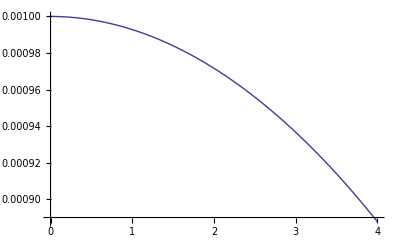

{{z→2.5×10^-7},{z→4.}}

{12.9885}

{15.7942}

{15.7942}

```mathematica
Clear[n0,n1,n4,n3,h,h0,z,C1,C2, A, B, c1, c2,coeffArrA,coeffArrB,a,d];
n[z_]= (n0 - n4 z^2 + n3 z- n1 (h0)^2 )
l = 0.001;
n0=1.37 ;
n1=0.01;
n3=0.04;
n4=0.01;
coeffArrA=RecurrenceTable[{a[n]==  (a[n-2]*(n4*(n-1)*(n-2)-2 n1)-a[n-1]*(n3(n-1)^2))/((n0- n1*l^2)*(n)*(n-1)),a[0]==1, a[1]== 0},a,{n,21}] ;
coeffArrB=RecurrenceTable[{b[n]==  (b[n-2]*(n4*(n)*(n-1)-2 n1)-b[n-1]*(n3((n)^2)))/((n0- n1*l^2)*(n+1)*(n)),b[0]==1,b[1]== (- n3)/(2*(n0- n1*l^2))},b,{n,21}];
h[z_]:=C2  (Expand[FromDigits[Reverse[coeffArrA],z]])+C1 z(Expand[FromDigits[Reverse[coeffArrB],z]]);
h[z];
k= (n3 - √(n3^2- 4 n4 n1 l^2))/(2 n4)
A[C1,C2]:= h[k];
B[C1,C2]:=h'[k];
sol9 = Solve[{A[C1,C2]== h0, B[C1,C2]==0},{C1,C2}]
c1 = C1/.sol9;
c2 = C2/.sol9;
C1=c1
C2=c2
h0=l;
Plot[h[z],{z,0,4}]
Sol2 =Solve[h[z]== √((-n4 z^2 + n3 z)/n1),z,Reals]
a=z/.Sol2[[1]];
c = z/.Sol2[[2]];
h[c];
-h0/(n0 h'[c])
(-h[c])/h'[c]
(-h[c])/h'[c]-(n3/n4-c)
```